# Driven damped pendulum

```mathematica
Quit[]
```

We set up a driven damped pendulum (DDP) as in Eq.12.11 with natural frequency ω_0 and driving frequency ω.The strength of the driving force is parameterized by γ =F_0/(m g). The drag coefficient is β.

```mathematica
deq=ϕ''[t]+2 β ϕ'[t]+ω0^2 Sin[ϕ[t]]==γ ω0^2 Cos[ω t]
```

ω0^2 Sin[ϕ[t]]+2 β ϕ'[t]+ϕ''[t]==γ ω0^2 Cos[t ω]

```mathematica
γ=0.2;
τ=1;
ω=(2 π)/τ;
ω0=1.5 ω;
β=ω0/4;
MI=2;
sol=Solve[ω0^2==mgL/MI,mgL];
mgL=mgL/.sol[[1]];
```

## Case 1: Small γ (approximately linear regime)

We'll go through a series of values of γ to observe the different behavior.

We'll plot phi in units where phi=1 is straight up, phi=2 is one full rotation, etc.

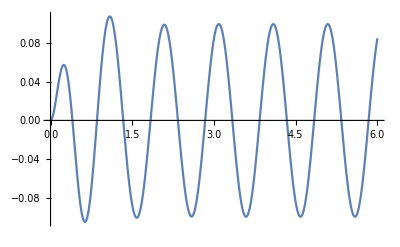

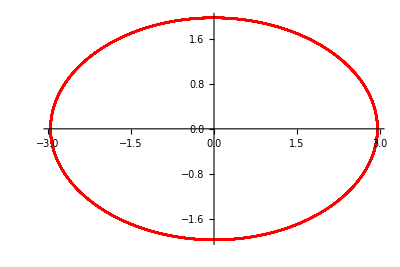

```mathematica
sol1=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,0,6}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,6}]
sol2=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,30,40}];
ϕ1[t_]=ϕ[t]/.sol2[[1]];
ParametricPlot[{ϕ1[t] √(mgL/2),ϕ1'[t] √(MI/2) },{t,30,40},PlotStyle->Red]
```

## Case 2: γ still in the regime of typical behavior

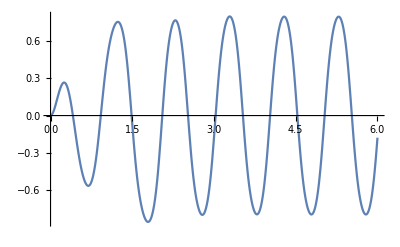

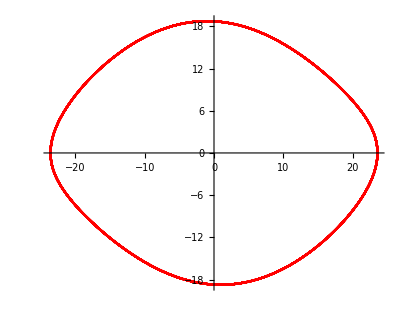

```mathematica
γ=0.9;
sol1=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,0,6}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,6}]
sol2=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,30,40}];
ϕ2[t_]=ϕ[t]/.sol2[[1]];
ParametricPlot[{ϕ2[t] √(mgL/2),ϕ2'[t] √(MI/2) },{t,30,40},PlotStyle->Red]
```

## Case 3: γ large enough to cause strange behavior: wild initial behavior, followed by period doubling

Note that the period (for returning to the original state) is 2T, as seen in the ϕ(t) and state-space plots that follow.

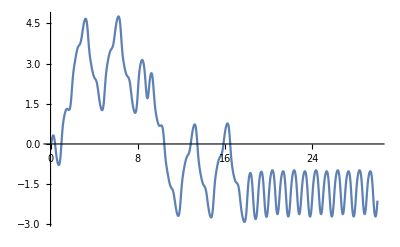

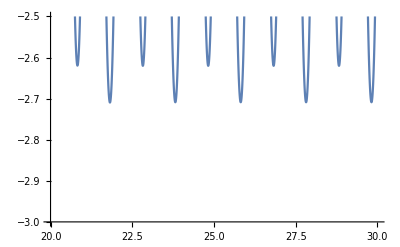

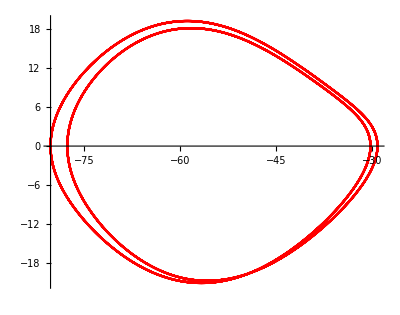

```mathematica
γ=1.073;
sol1=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,0,30}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,30}]
Plot[(ϕ[t]/.sol1[[1]])/π,{t,20,30},PlotRange->{-3,-2.5}]
sol3=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,30,40}];
ϕ3[t_]=ϕ[t]/.sol3[[1]];
ParametricPlot[{ϕ3[t] √(mgL/2),ϕ3'[t] √(MI/2) },{t,30,40},PlotStyle->Red]
```

## Case 4: Period tripling

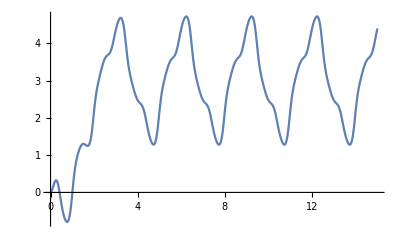

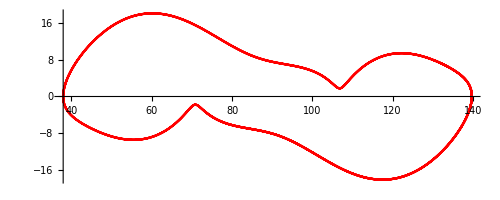

```mathematica
γ=1.077;
sol1=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,0,15}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,15}]
sol4=NDSolve[{deq,ϕ[0]==0,ϕ'[0]==0},ϕ[t],{t,30,40}];
ϕ4[t_]=ϕ[t]/.sol4[[1]];
ParametricPlot[{ϕ4[t] √(mgL/2),ϕ4'[t] √(MI/2) },{t,30,40},PlotStyle->Red]
```

## Case 5: Multiple attractors; initial conditions determine which one is selected

Same as the last case, but with different initial conditions.

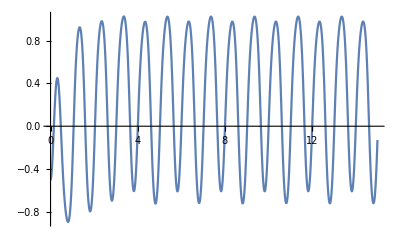

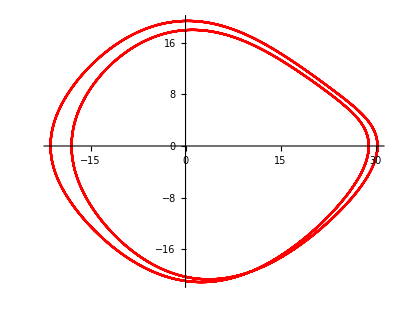

```mathematica
γ=1.077;
sol1=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,0,15}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,15}]
sol5=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,30,40}];
ϕ5[t_]=ϕ[t]/.sol5[[1]];
ParametricPlot[{ϕ5[t] √(mgL/2),ϕ5'[t] √(MI/2) },{t,30,40},PlotStyle->Red]
```

## Case 6: Slightly larger γ; quadrupled period

Period 4.

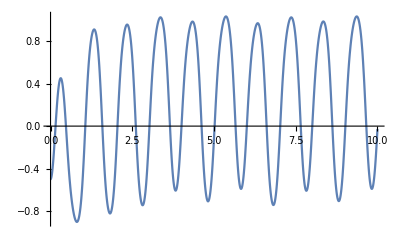

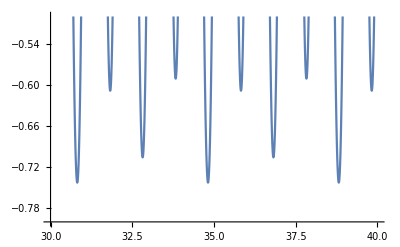

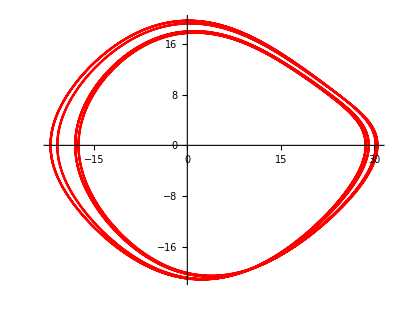

```mathematica
γ=1.081;
sol1=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,0,10}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,10}]
sol7=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,30,40}];
ϕ7[t_]=ϕ[t]/.sol7[[1]];
Plot[ϕ7[t]/π,{t,30,40},PlotRange->{-0.8,-0.5}]
ParametricPlot[{ϕ7[t] √(mgL/2),ϕ7'[t] √(MI/2) },{t,30,40},PlotStyle->Red]
```

## Case 7: Period doubling cascade continues

Period 8.

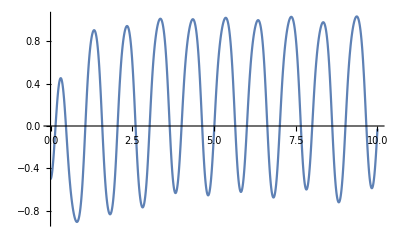

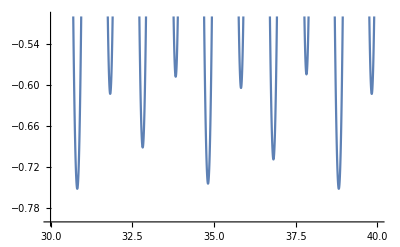

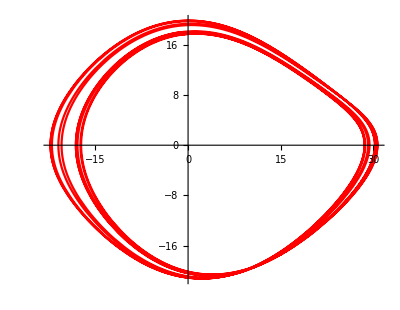

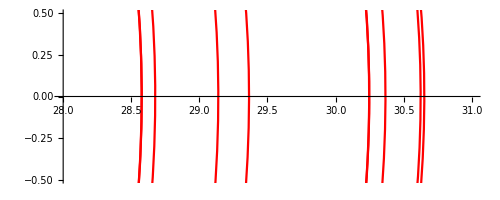

```mathematica
γ=1.0826;
sol1=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,0,10}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,10}]
sol8=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,30,40}];
ϕ8[t_]=ϕ[t]/.sol8[[1]];
Plot[ϕ8[t]/π,{t,30,40},PlotRange->{-0.8,-0.5}]
ParametricPlot[{ϕ8[t] √(mgL/2),ϕ8'[t] √(MI/2) },{t,30,40},PlotStyle->Red]
ParametricPlot[{ϕ8[t] √(mgL/2),ϕ8'[t] √(MI/2) },{t,30,40},PlotStyle->Red,PlotRange->{{28,31},{-0.5,+0.5}}]
```

## Case 8: γ beyond the threshold for infinite period

The onset of chaos.

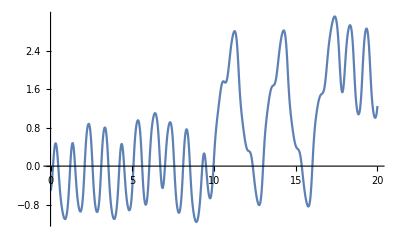

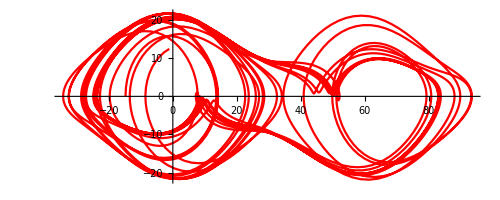

```mathematica
γ=1.151;
sol1=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,0,20}];
Plot[(ϕ[t]/.sol1[[1]])/π,{t,0,20}]
sol10=NDSolve[{deq,ϕ[0]==-π/2,ϕ'[0]==0},ϕ[t],{t,0,40}];
ϕ10[t_]=ϕ[t]/.sol10[[1]];
ParametricPlot[{ϕ10[t] √(mgL/2),ϕ10'[t] √(MI/2) },{t,0,40},PlotStyle->Red]
```